```mathematica
DateString[]
```

Wed 25 Jun 2014 15:24:49

```mathematica
Clear["Global`*"]
```

# Figure1:CoESS and Superinfection

Notebook pour résolution des CoESS pour différentes valeurs de σ

```mathematica
s[x_]:=Subscript[s, max]/(1+b Exp[-c x])/.c->  σ1/σ^2 Subscript[s, max]/b  /.b->Subscript[s, max]/σ-1/.Subscript[s, max]->10//Simplify;
para=β'[α]-(β[α](1-2 h σ1))/(μ+α+γ+σ h);
hote2=r'[γ]+(r[γ]-μ)/(μ+α+γ+h);
res = Solve[
  {0 == r[γ](x+y)-(μ+(β[α] y)) x+γ y,
   0 ==β[α] x y-(μ+α+γ )y}, {x, y}];
eqlib=res[[1]];
Ieq=y/.eqlib[[2]]/.α[w]->α/.γ[w]->γ/.β[w]->β[α];

β[α_]:=Subscript[β, 0] α/(1+α)
r[γ_]:=Subscript[r, m]/(1+c γ)

isop1=(γ/.(Solve[0==para/.h->β[α]Ieq,γ])[[1]])//Simplify;
isop2=(γ/.(Solve[0==para/.h->β[α]Ieq,γ])[[2]])//Simplify;
isoh=(γ/.Solve[0==hote2/.h->β[α]Ieq,γ])[[2]]//Simplify;
```

### Résolution pour σ=0

```mathematica
plotvir=Plot[isop1/.{c->0.05,μ->1,σ->0,σ1->0,Subscript[r, m]->2},{α,1,5},PlotStyle->{Black,Thickness[0.0035]}];
plotgam=Plot[isoh/.{c->0.05,μ->1,σ->0,σ1->0,Subscript[r, m]->2},{α,0,10},PlotStyle->{Black,Thickness[0.005]}];
```

### Résolution pour σ=1

```mathematica
plotvir1=Plot[isop1/.{c->0.05,μ->1,σ->1,σ1->0,Subscript[r, m]->2},{α,1,5},PlotStyle->{Thickness[0.004],Dashed,Black} ];
```

### Résolution pour σ=6

```mathematica
plotvir6=Plot[isop1/.{c->0.05,μ->1,σ->6,σ1->0,Subscript[r, m]->2},{α,1,5},PlotStyle->{Thickness[0.004],DotDashed,Black} ];
```

### Dessin de la figure

```mathematica
front=Plot[(rm/(μ+α[w])-1)/c/.{Subscript[β, 0]-> 10,c->0.05,rm->2,σ-> 1,μ->1},{α[w],0,4},PlotStyle->{GrayLevel[0.8]},PlotRange->{0,8},Filling->Bottom,FillingStyle->GrayLevel[0.8]];
```

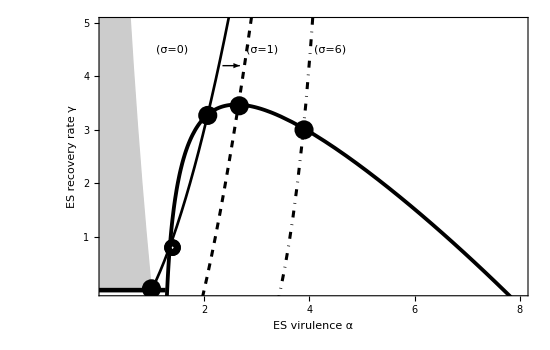

```mathematica
With[{epsFontSize=13,xcoords={1.4,4.5}},textsigma0=Style[Inset[Cell[TextData[Cell[BoxData[FormBox[SubscriptBox["σ=0",""],TraditionalForm]]]]],xcoords,{Left,Baseline}],FontWeight->Normal,FontSize->epsFontSize];];
With[{epsFontSize=13,xcoords={3.1,4.5}},textsigma1=Style[Inset[Cell[TextData[Cell[BoxData[FormBox[SubscriptBox["σ=1",""],TraditionalForm]]]]],xcoords,{Left,Baseline}],FontWeight->Normal,FontSize->epsFontSize];];
With[{epsFontSize=13,xcoords={4.4,4.5}},textsigma2=Style[Inset[Cell[TextData[Cell[BoxData[FormBox[SubscriptBox["σ=6",""],TraditionalForm]]]]],xcoords,{Left,Baseline}],FontWeight->Normal,FontSize->epsFontSize];];label3= "ES virulence α";label4="ES recovery rate γ";
textdataplot=Show[front,plotgam,plotvir,plotvir1,plotvir6,ListPlot[{{2.67,3.45}},PlotStyle->{Black,PointSize[0.025]}],Graphics[{Thickness[0.006],Line[{{0,0.005},{1.27,0.005}}]}],Graphics[{Arrowheads[0.03],Arrow[{{2.35,4.2},{2.68,4.2}}]}], ListPlot[{{2.07,3.27},{1,0.03},{3.9,3}},PlotStyle->{Black,PointSize[0.025]}],ListPlot[{{1.4,0.8}},PlotStyle->Black,PlotMarkers-> Graphics[{Thickness[0.35],Circle[]},ImageSize-> 10]],PlotRange-> {{0.16,8},{0,5}},Ticks->{{0,2,4,6,8},{1,2,3,4,5}},Frame->{{True,False},{True,False}}, TextStyle-> {"Helvetica",FontSize-> 15},LabelStyle->Directive[FontFamily->"Helvetica",FontSize-> 15],FrameLabel->{label3,label4}, FrameTicks->{{0,1,2,3,4,5,6,7,8},{1,2,3,4,5},{},{}},Epilog->{textsigma0,textsigma1,textsigma2},AspectRatio->Automatic]
```

```mathematica
Export["superetsans4.pdf",%2250,"PDF"]
```

superetsans4.pdf

```mathematica
(*exportation en pdf car les lettres grecques sont altérées en format eps*)
```